```mathematica
SetDirectory[NotebookDirectory[]];
Get["../lib/lib2.m"];
Get["../lib/util.m"];
```

```mathematica
<<MaTeX`;
```

```mathematica
SetOptions[MaTeX,"Preamble"->{"\\usepackage{physics,mathtools}"}];
texStyle={FontFamily->"Latin Modern Roman",FontSize->12};
plotsDir = "../../plots/plots-102-hist";
If[!DirectoryQ[plotsDir], CreateDirectory[plotsDir]];
```

```mathematica
data[1] = Import["../../runs/Trials/N8K9/12873160.dat"];
data[2] = Import["../../runs/Trials/N8K9/85145990.dat"];
data[3] = Import["../../runs/Trials/N8K9/93249996.dat"];
```

```mathematica
Evaluate[Array[rad, 3]] = (radius/@data[#]&)/@Range[3];
```

$Aborted

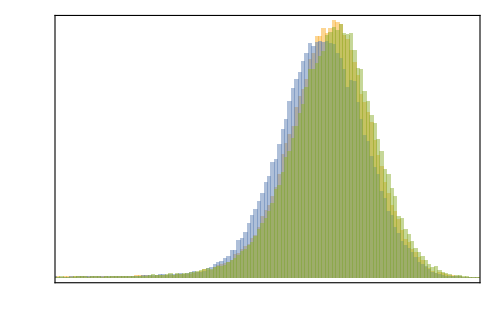

```mathematica
plt1 = Histogram[{rad[1][[All, 2]], rad[2][[All,2]], rad[3][[All,2]]}, 500,"PDF",
ChartLegends->MaTeX[{"a", "b", "c"}, "DisplayStyle"->False],
Frame->True,
FrameStyle->Black,
FrameLabel->MaTeX[{"\\Tr X^2", "\\rho"}],
BaseStyle->texStyle,
FrameTicks->{{With[{ticks = Range[0.0, 3.5, 0.5]}, Thread[{ticks, MaTeX[ticks, "DisplayStyle"->False]}]], None}, {With[{ticks = Range[1.8, 3.0, 0.2]}, Thread[{ticks, MaTeX[ticks, "DisplayStyle"->False]}]], None}},
Axes->False,
PlotRange->{{1.8, 3.0}, Automatic},
ImageSize->500
];
(*Export[plotsDir<>"/histogram-T-10000.pdf", plt1];*)
plt1
```

```mathematica
𝒟[1] = FindDistribution[rad[1][[All, 2]]]
```

StudentTDistribution[2.58846,0.0965066,2.96032]

```mathematica
𝒟[2] = FindDistribution[rad[2][[All, 2]]]
```

LogisticDistribution[2.56894,0.0814447]

```mathematica
𝒟[3] = FindDistribution[rad[3][[All, 2]]]
```

LogisticDistribution[2.58831,0.0745708]

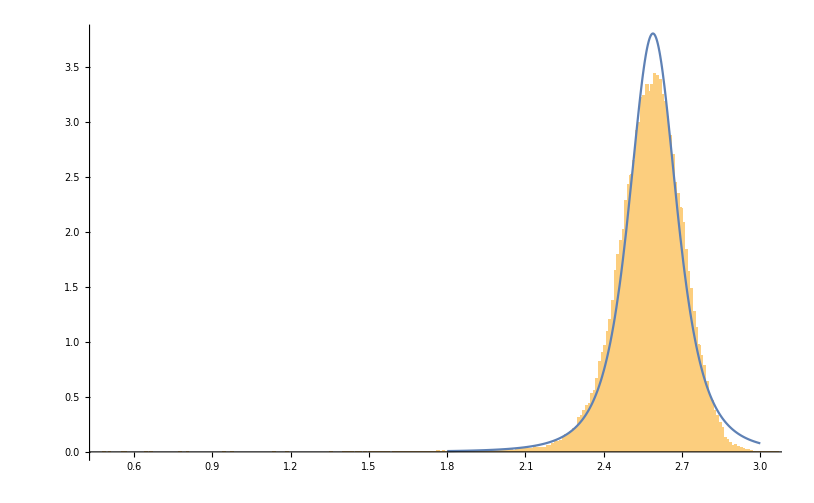

```mathematica
Show[Histogram[rad[1][[All, 2]], 400, "PDF"], Plot[PDF[𝒟[1]][x], {x, 1.8, 3.0}]]
```

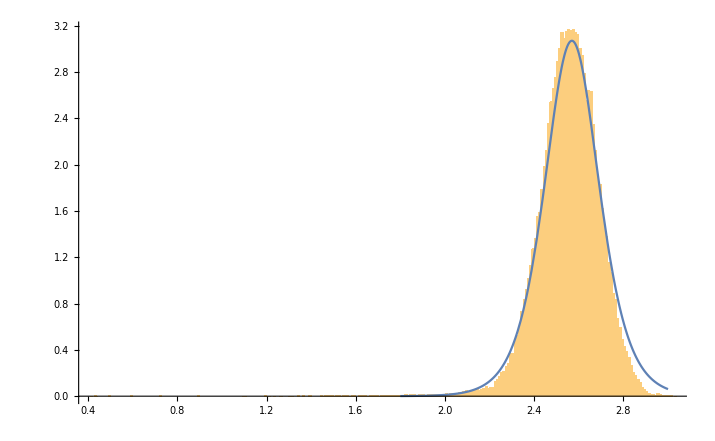

```mathematica
Show[Histogram[rad[2][[All, 2]], 400, "PDF"], Plot[PDF[𝒟[2]][x], {x, 1.8, 3.0}]]
```

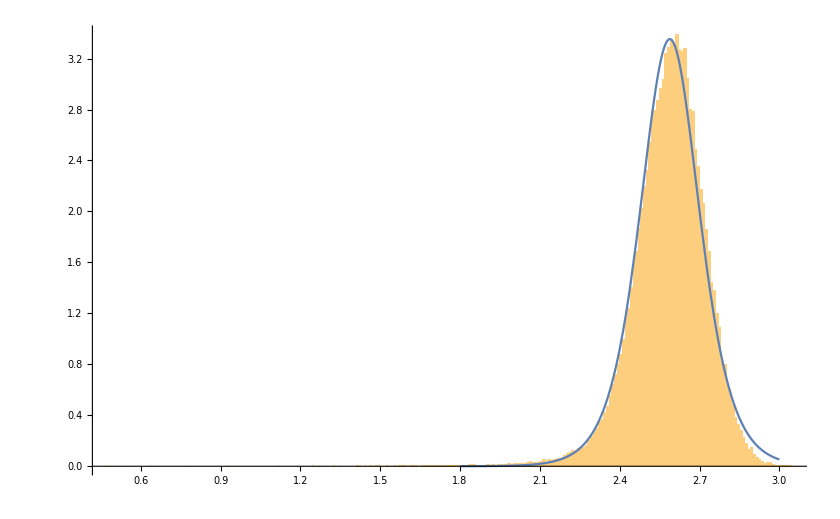

```mathematica
Show[Histogram[rad[3][[All, 2]], 400, "PDF"], Plot[PDF[𝒟[3]][x], {x, 1.8, 3.0}]]
```

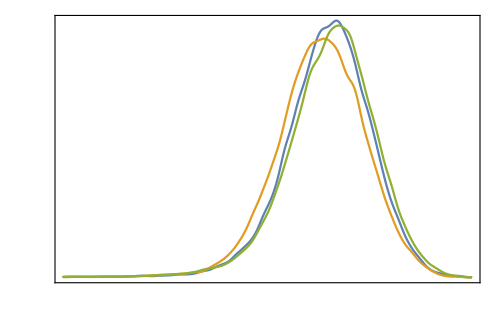

```mathematica
plt2 = SmoothHistogram[{rad[1][[All, 2]], rad[2][[All,2]], rad[3][[All,2]]},
PlotLegends->MaTeX[{"a", "b", "c"}, "DisplayStyle"->False],
Frame->True,
FrameStyle->Black,
FrameLabel->MaTeX[{"\\Tr X^2", "\\rho"}],
BaseStyle->texStyle,
FrameTicks->{{With[{ticks = Range[0.0, 3.5, 0.5]}, Thread[{ticks, MaTeX[ticks, "DisplayStyle"->False]}]], None}, {With[{ticks = Range[1.8, 3.0, 0.2]}, Thread[{ticks, MaTeX[ticks, "DisplayStyle"->False]}]], None}},
Axes->False,
PlotRange->{{1.8, 3.0}, Automatic},
ImageSize->500
];
Export[plotsDir<>"/smooth-histogram-T-10000.pdf", plt2];
plt2
```